{{1.,0.95238,4.41632×10^-9},{0.5,1.00433,0.00125211},{0.333333,1.02089,0.00281368},{0.25,1.00022,0.00622808},{0.2,1.00111,0.0100562}}

{{1.,0.381702,0.000365611},{0.5,0.41707,0.00125848},{0.333333,0.462404,0.00266334},{0.25,0.460758,0.00580976},{0.2,0.476495,0.00908413}}

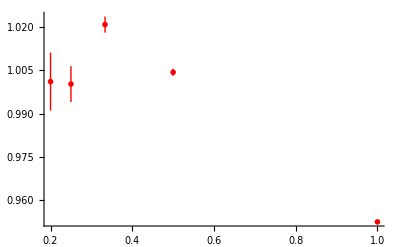

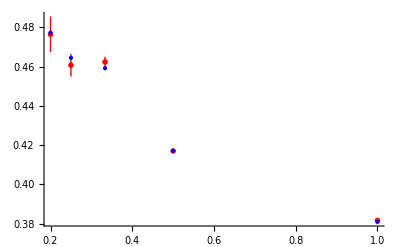

```mathematica
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
SUNData=GetConvergenceData["G:\\LAT\\sd_metropolis\\data\\pcm_sc_mspace\\scalars_d1_t2_s1_l4.0000_rsm.dat",1,2,0.0,1.0,10]
LinkData=GetConvergenceData["G:\\LAT\\sd_metropolis\\data\\pcm_sc_mspace\\scalars_d1_t2_s1_l4.0000_rsm.dat",1,4,0.0,1.0,10]
RCANData={{1/1,0.38095238095238093},{1/2,0.41715128984322375},{1/3,0.45920358337341727},{1/4,0.46448009338131374},{1/5,0.4773704921241454}};
PlotWithErrors[SUNData,Red]
Gr1=PlotWithErrors[LinkData,Red];
Gr2=ListPlot[RCANData,PlotStyle->{Blue}];
Show[Gr1,Gr2]
```

```mathematica
N[1/4+1/32]
```

0.28125